```mathematica
Clear[data]
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["PhysicalConstants`"];
ch=PlanckConstant/(Joule Second);
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
metaStructure=Join[{Word,Word},Table[Real,{k,1,102}]];
data=Import["operahouse.edm"];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

{1}
 |  |  |  |

```mathematica
ListPlot[]
```

Part::partw: Part 9 of {""} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ListPlot::lpn: {« 1 »} ⟦ 1 ;; All, 9 ⟧ is not a list of numbers or pairs of numbers.

Part::partw: Part 9 of {""} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ListPlot::lpn: {« 1 »} ⟦ 1 ;; All, 9 ⟧ is not a list of numbers or pairs of numbers.

ListPlot[{1}⟦1;;All,9⟧]
 |  |  |  |

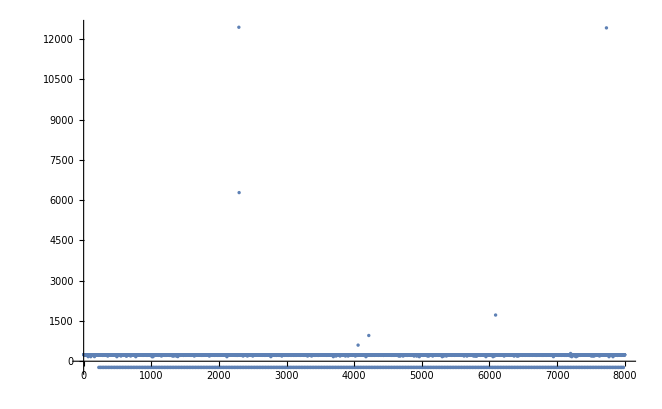

```mathematica
ListPlot[Table[data[[1;;8000,k]],{k,50,50}]]
```

```mathematica
data[[104,9]]
```

1257

```mathematica
data[[15600;;15750,9]]
```

Part::partw: Part 9 of {""} does not exist.

$Aborted[]